```mathematica
Exit
```

```mathematica
Needs["PM`"]
LoadPackages[{"Geometries"}]
```

LoadPackages: Loading of GeneralTools leaked 1 symbols:

{dims$}

```mathematica
M=CliffordTorusMesh[Mesh->{30,10}2 2 ]
```

mesh[…]

```mathematica
λ=Total[x^2];
Table[2Indexed[x,i]Indexed[x,j]-Boole[i==j]Sum[Indexed[x,i]^2,{i,1,3}],{i,1,3},{j,1,3}]//InputForm
```

```mathematica
{{
Indexed[x, {1}]^2 - Indexed[x, {2}]^2 - Indexed[x, {3}]^2, 
  2*Indexed[x, {1}]*Indexed[x, {2}], 2*Indexed[x, {1}]*
   Indexed[x, {3}]}, {2*Indexed[x, {1}]*Indexed[x, {2}], 
  -Indexed[x, {1}]^2 + Indexed[x, {2}]^2 - Indexed[x, {3}]^2, 
  2*Indexed[x, {2}]*Indexed[x, {3}]}, 
 {2*Indexed[x, {1}]*Indexed[x, {3}], 2*Indexed[x, {2}]*Indexed[x, {3}], 
  -Indexed[x, {1}]^2 - Indexed[x, {2}]^2 + Indexed[x, {3}]^2}}
```

```mathematica
(*Fundamental vector fields of Moebius group that are transversal to similarity transformations.*)
U=x↦{Indexed[x,1]^2-Indexed[x,2]^2-Indexed[x,3]^2,2 Indexed[x,1] Indexed[x,2],2 Indexed[x,1] Indexed[x,3]};
V=x↦{2 Indexed[x,1] Indexed[x,2],-Indexed[x,1]^2+Indexed[x,2]^2-Indexed[x,3]^2,2 Indexed[x,2] Indexed[x,3]};
W=x↦{2 Indexed[x,1] Indexed[x,3],2 Indexed[x,2] Indexed[x,3],-Indexed[x,1]^2-Indexed[x,2]^2+Indexed[x,3]^2};
```

```mathematica
"U[x]"->MatrixForm[U[x]]
"V[x]"->MatrixForm[V[x]]
"W[x]"->MatrixForm[W[x]]
```

U[x]→(x1^2-x2^2-x3^2
2 x1 x2
2 x1 x3)

V[x]→(2 x1 x2
-x1^2+x2^2-x3^2
2 x2 x3)

W[x]→(2 x1 x3
2 x2 x3
-x1^2-x2^2+x3^2)

```mathematica
(*general parameterized Torus of revolution with circular contour*)
Φ=X↦{
Cos[Indexed[X,1]](R+r Cos[Indexed[X,2]]),
Sin[Indexed[X,1]](R+r Cos[Indexed[X,2]]),
r Sin[Indexed[X,2]]
};
"Parameterized torus"->MatrixForm[Φ[{ϕ,θ}]]
ν=D[Φ[{ϕ,θ}],r];
"surface normal = L^2-gradient of volume"->MatrixForm[ν]

g=#ᵀ.#&[D[Φ[{ϕ,θ}],{{ϕ,θ},1}]]//Simplify;
"pullback metric in local coordinates"->MatrixForm[g]
vol=Simplify[Sqrt[Det[g]],{r>0,R>0}];
"volume density in local coordinates"->vol
```

Parameterized torus→((R+r Cos[θ]) Cos[ϕ]
(R+r Cos[θ]) Sin[ϕ]
r Sin[θ])

surface normal = L^2-gradient of volume→(Cos[θ] Cos[ϕ]
Cos[θ] Sin[ϕ]
Sin[θ])

pullback metric in local coordinates→((R+r Cos[θ])^2 | 0
0 | r^2)

volume density in local coordinates→r √((R+r Cos[θ])^2)

```mathematica
(*This to shows that all three fundamental vector fields U, V, W are L^2-orthogonal to the L^2-gradient of volume. These are the integrants:*)
intU=ν.U[Φ[{ϕ,θ}]] vol//Simplify
intV=ν.V[Φ[{ϕ,θ}]]vol//Simplify
intW=ν.W[Φ[{ϕ,θ}]]vol//Simplify
```

r √((R+r Cos[θ])^2) (2 r R+(r^2+R^2) Cos[θ]) Cos[ϕ]

r √((R+r Cos[θ])^2) (2 r R+(r^2+R^2) Cos[θ]) Sin[ϕ]

r (r^2-R^2) √((R+r Cos[θ])^2) Sin[θ]

```mathematica
"L^2 inner product of ν and U"->Integrate[Integrate[intU,{ϕ,-Pi,Pi}],{θ,-Pi,Pi}]
"L^2 inner product of ν and V"->Integrate[Integrate[intV,{ϕ,-Pi,Pi}],{θ,-Pi,Pi}]
"L^2 inner product of ν and W"->Integrate[Integrate[(intW/.{θ->θ})+(intW/.{θ->-θ}),{θ,0,Pi}],{ϕ,-Pi,Pi}]
```

L^2 inner product of ν and U→0

L^2 inner product of ν and V→0

L^2 inner product of ν and W→0

```mathematica
(*We don't even have to compute the mean curvature vector H -- it suffices to know that H[ϕ,θ]=h[θ] ν and that h[-θ]==h[θ]!*)

intHU=h[θ]ν.U[Φ[{ϕ,θ}]]vol//Simplify
intHV=h[θ]ν.V[Φ[{ϕ,θ}]]vol//Simplify
intHW=h[θ]ν.W[Φ[{ϕ,θ}]]vol//Simplify

"L^2 inner product of H and U"->Integrate[Integrate[intHU,{ϕ,-Pi,Pi}],{θ,-Pi,Pi}]
"L^2 inner product of H and V"->Integrate[Integrate[intHV,{ϕ,-Pi,Pi}],{θ,-Pi,Pi}]
"L^2 inner product of H and W"->Integrate[Integrate[Simplify[intHW+(intHW/.θ->-θ),h[-θ]==h[θ]],{θ,0,Pi}],{ϕ,-Pi,Pi}]
```

r √((R+r Cos[θ])^2) (2 r R+(r^2+R^2) Cos[θ]) Cos[ϕ] h[θ]

r √((R+r Cos[θ])^2) (2 r R+(r^2+R^2) Cos[θ]) h[θ] Sin[ϕ]

r (r^2-R^2) √((R+r Cos[θ])^2) h[θ] Sin[θ]

L^2 inner product of H and U→0

L^2 inner product of H and V→0

L^2 inner product of H and W→0

```mathematica
M=TorusMesh[5,1,Mesh->{30,10}2 2 2];
```

```mathematica
AppendToConstraintList[M,Area];
AppendToConstraintList[M,VolumePotential];
U=SpecialConformalVectorFields[M];
{u,v,w}=Partition[#,3]&/@U;
U1=RotationVectorFields[M];
{u1,v1,w1}=Partition[#,3]&/@U1;
```

```mathematica
A=Constraint'[M];
A.U[[1]]
A.U[[2]]
A.U[[3]]
```

{2.01584×10^-11,1.50867×10^-11}

{1.428×10^-10,1.06764×10^-10}

{1.4892×10^-12,8.89289×10^-13}

```mathematica
t=0.1;
```

mesh[…]

```mathematica
t=0.000000001;
Mt=Displace[M,t u];
Area[Mt]-Area[M]-t Area'[M].Flatten[u]
```

5.68434×10^-14

```mathematica
DotThread[u,u]==DotThread[v,v]==DotThread[w,w]
```

True

```mathematica
OpenSource@RotationVectorFields
```

```mathematica
OpenSource@MeshGradientOperator
```

```mathematica
SparseArray[1./EdgeLengths[M]] SignedAdjacencyMatrix[M,Triangles,Vertices]
```

0.422364 s elapsed while compiling cNorm3.

Writing to /Users/Henrik/Library/Mathematica/Applications/GeneralTools/LibraryResources/MacOSX-x86-64/cNorm3.dylib.

SparseArray[…]

```mathematica
MeshDerivativeOperator[M]
```

SparseArray[<83538>, {27846, 4641}]

```mathematica
TriangleCount[M] 3
```

27846

```mathematica
M=TorusMesh[5,1,Mesh->{30,10}2 2 2 2];
U=SpecialConformalVectorFields[M];
{u,v,w}=Partition[#,3]&/@U;
```

```mathematica
A=ArrayReshape[MeshDerivativeOperator[M].u,{TriangleCount[M],3,3}];
```

```mathematica
AT=Transpose[A,{1,3,2}];
```

```mathematica
a=(Eigenvalues/@DotThread[AT,A])[[All,1;;2]];
b=(Eigenvalues/@DotThread[A,AT])[[All,1;;2]];
```

```mathematica
Max[a[[All,1]]-a[[All,2]]]
```

143.953

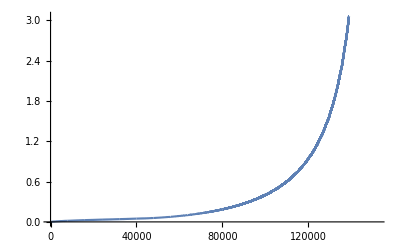

-Graphics-

```mathematica
ListLinePlot[Sort[a[[All,1]]/a[[All,2]]-1]]
ListLinePlot[Sort[b[[All,1]]/b[[All,2]]-1]]
```

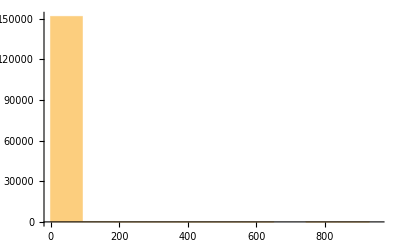

-Graphics-

```mathematica
Histogram[a[[All,1]]/a[[All,2]]-1]
Histogram[b[[All,1]]/b[[All,2]]-1]
```

```mathematica
A[[1]]//MatrixForm
```

(0.106805 | -0.310082 | -0.958388
-0.630484 | 11.9751 | -0.0253073
-1.11679 | -0.0759765 | 11.88)

{{{0.106805,-0.310082,-0.958388},{-0.630484,11.9751,-0.0253073},{-1.11679,-0.0759765,11.88}},9280,{{1},{1},{1}}}
 |  |  |  |

```mathematica
u//Dimensions
```

{4641,3}

```mathematica
OpenSource@MeshDerivativeOperator
```

OpenSource::morethanone: More than one source found. Please specify which one to open by calling OpenSource[M,MeshDerivativeOperator,n].

1 | → | <|File→/Users/Henrik/Dropbox/Mathematica/PackageSources/Mesh/MeshDerivativeOperator.nb,Cell→3|>
2 | → | <|File→/Users/Henrik/Dropbox/Mathematica/PackageSources/Polygon/MeshDerivativeOperator.nb,Cell→4|>

```mathematica
MeshGradientOperator[M]
```

MeshGradientOperator[mesh[…]]

```mathematica
StabilizationReferencePoint[M]
```

{-2.53583×10^-14,-1.81383×10^-13,-1.85665×10^-15}

```mathematica
DotThread[u1,u1]
DotThread[v1,v1]
```

```mathematica
Max[Abs[DotThread[u,v]]]
Max[Abs[DotThread[v,w]]]
Max[Abs[DotThread[w,u]]]
```

5.00711×10^-13

1.13687×10^-13

1.13687×10^-13

0.470906 s elapsed while compiling getRotationGenerators.

Writing to /Users/Henrik/Library/Mathematica/Applications/GenericMesh/LibraryResources/MacOSX-x86-64/getRotationGenerators.dylib.

{{-1.81383×10^-13,6.,0.,-0.316652,5.99164,0.,-0.632422,5.96658,13908,0.,0.631057,5.9537,0.,0.315969,5.97871,0.},1,{1}}
 |  |  |  |

```mathematica
Max[Abs[DotThread[u,i]]]
```

```mathematica
Max[Abs[DotThread[u,v]]]
Max[Abs[DotThread[u,v]]]
```

5.00711×10^-13

```mathematica
Show[
MeshPlot[M],
FieldPlot[M,0.2u]
]
```

-Graphics3D-

2.01599×10^-11

197.121

mesh[…]

```mathematica
A
```

SparseArray[…]

```mathematica
Show[
MeshPlot[M],
FieldPlot[M,w]
]
```

-Graphics3D-

```mathematica
Partition[#,3]&/@SpecialConformalVectorFields[M]//Dimensions
```

{3,4641,3}

```mathematica
GridMeshPlot[M]
```

-Graphics3D-

```mathematica
a=.
b=.
```

T

```mathematica
X=.
```

```mathematica
Exit
```

```mathematica
ClearAll[a1,a2,a3,b1,b2,b3];
xx=Table[Indexed[x,i],{i,1,3}];
aa={a1[t],a2[t],a3[t]};
bb={b1[t],b2[t],b3[t]}
p=1;
(*A=IdentityMatrix[3];*)
AA={{A11[t],A12[t],A13[t]},{A21[t],A22[t],A23[t]},{A31[t],A32[t],A33[t]}};
(*AA=RandomVariate[CircularRealMatrixDistribution[3]]*)
f=x↦Evaluate[bb+α[t] AA.(xx-aa)/Dot[xx-aa,xx-aa]^p];
```

{b1[t],b2[t],b3[t]}

```mathematica
f[xx/xx.xx]/.t->0//Simplify
```

{x1,x2,x3}

```mathematica
f[xx]/f[xx].f[xx]//Simplify
```

```mathematica
bla=f[xx/xx.xx]//Simplify;
```

```mathematica
blubb=Numerator/@(bla-xx/.t->0//Together);
```

```mathematica
CoefficientRules[blubb,xx]//Simplify
```

{{},{},{}}

```mathematica
A11'[0]=0;
A22'[0]=0;
A33'[0]=0;
A21'[0]=-A12'[0];
A31'[0]=-A13'[0];
A32'[0]=-A23'[0];
```

```mathematica
ClearAll[Derivative]
```

```mathematica
k=D[bla,t]/.t->0//Together
```

{x1^2 a1'[0]-x2^2 a1'[0]-x3^2 a1'[0]+x2 A12'[0]+x3 A13'[0]+2 x1 x2 a2'[0]+2 x1 x3 a3'[0]+b1'[0]+x1 α'[0],2 x1 x2 a1'[0]-x1 A12'[0]-x1^2 a2'[0]+x2^2 a2'[0]-x3^2 a2'[0]+x3 A23'[0]+2 x2 x3 a3'[0]+b2'[0]+x2 α'[0],2 x1 x3 a1'[0]-x1 A13'[0]+2 x2 x3 a2'[0]-x2 A23'[0]-x1^2 a3'[0]-x2^2 a3'[0]+x3^2 a3'[0]+b3'[0]+x3 α'[0]}

```mathematica
k/.{b1'[0]->0,b2'[0]->0,b3'[0]->0,α'[0]->0,A12'[0]->0,A13'[0]->0,A23'[0]->0,
a1'[0]->0,a2'[0]->0,a3'[0]->1}
```

{2 x1 x3,2 x2 x3,-x1^2-x2^2+x3^2}

```mathematica
λ=Total[xx^2];
{U,V,W}=Table[2Compile`GetElement[xx,i]Compile`GetElement[xx,j]-Boole[i==j]λ,{i,1,Length[xx]},{j,1,Length[xx]}];
```

```mathematica
W
```

{2 x1 x3,2 x2 x3,-x1^2-x2^2+x3^2}

```mathematica
{U,V,W}//Transpose//MatrixForm
```

(x1^2-x2^2-x3^2 | 2 x1 x2 | 2 x1 x3
2 x1 x2 | -x1^2+x2^2-x3^2 | 2 x2 x3
2 x1 x3 | 2 x2 x3 | -x1^2-x2^2+x3^2)

```mathematica
/
```

```mathematica
eq=D[bla,t]-Identity[3]/.t->0//Together
```

{-3+x1^2 a1'[0]-x2^2 a1'[0]-x3^2 a1'[0]+x1 A11'[0]+x2 A12'[0]+x3 A13'[0]+2 x1 x2 a2'[0]+2 x1 x3 a3'[0]+b1'[0]+x1 α'[0],-3+2 x1 x2 a1'[0]-x1^2 a2'[0]+x2^2 a2'[0]-x3^2 a2'[0]+x1 A21'[0]+x2 A22'[0]+x3 A23'[0]+2 x2 x3 a3'[0]+b2'[0]+x2 α'[0],-3+2 x1 x3 a1'[0]+2 x2 x3 a2'[0]-x1^2 a3'[0]-x2^2 a3'[0]+x3^2 a3'[0]+x1 A31'[0]+x2 A32'[0]+x3 A33'[0]+b3'[0]+x3 α'[0]}

```mathematica
CoefficientRules[eq,xx]
```

{{{2,0,0}→a1'[0],{1,1,0}→2 a2'[0],{1,0,1}→2 a3'[0],{1,0,0}→A11'[0]+α'[0],{0,2,0}→-a1'[0],{0,1,0}→A12'[0],{0,0,2}→-a1'[0],{0,0,1}→A13'[0],{0,0,0}→-3+b1'[0]},{{2,0,0}→-a2'[0],{1,1,0}→2 a1'[0],{1,0,0}→A21'[0],{0,2,0}→a2'[0],{0,1,1}→2 a3'[0],{0,1,0}→A22'[0]+α'[0],{0,0,2}→-a2'[0],{0,0,1}→A23'[0],{0,0,0}→-3+b2'[0]},{{2,0,0}→-a3'[0],{1,0,1}→2 a1'[0],{1,0,0}→A31'[0],{0,2,0}→-a3'[0],{0,1,1}→2 a2'[0],{0,1,0}→A32'[0],{0,0,2}→a3'[0],{0,0,1}→A33'[0]+α'[0],{0,0,0}→-3+b3'[0]}}

```mathematica
a1[0]=0;
a2[0]=0;
a3[0]=0;

b1[0]=0;
b2[0]=0;
b3[0]=0;
α[0]=1;
A11[0]=1;
A12[0]=0;
A13[0]=0;
A21[0]=0;
A22[0]=1;
A23[0]=0;
A31[0]=0;
A32[0]=0;
A33[0]=1;
```

```mathematica
d
```

d

```mathematica
f
```

Function[x,{b1[t]+((A11 (x1-a1[t])+A12 (x2-a2[t])+A13 (x3-a3[t])) α[t])/((x1-a1[t])^2+(x2-a2[t])^2+(x3-a3[t])^2),b2[t]+((A21 (x1-a1[t])+A22 (x2-a2[t])+A23 (x3-a3[t])) α[t])/((x1-a1[t])^2+(x2-a2[t])^2+(x3-a3[t])^2),b3[t]+((A31 (x1-a1[t])+A32 (x2-a2[t])+A33 (x3-a3[t])) α[t])/((x1-a1[t])^2+(x2-a2[t])^2+(x3-a3[t])^2)}]

```mathematica
f[aa]//Simplify
```

{b1[t]+((A11 x1+A12 x2+A13 x3-A11 a1[t]-A12 a2[t]-A13 a3[t]) α[t])/((x1-a1[t])^2+(x2-a2[t])^2+(x3-a3[t])^2),b2[t]+((A21 x1+A22 x2+A23 x3-A21 a1[t]-A22 a2[t]-A23 a3[t]) α[t])/((x1-a1[t])^2+(x2-a2[t])^2+(x3-a3[t])^2),b3[t]+((A31 x1+A32 x2+A33 x3-A31 a1[t]-A32 a2[t]-A33 a3[t]) α[t])/((x1-a1[t])^2+(x2-a2[t])^2+(x3-a3[t])^2)}

```mathematica
f[xx/xx.xx]//Simplify
```

{b1[t]+((A11 x1+A12 x2+A13 x3-A11 a1[t]-A12 a2[t]-A13 a3[t]) α[t])/((x1-a1[t])^2+(x2-a2[t])^2+(x3-a3[t])^2),b2[t]+((A21 x1+A22 x2+A23 x3-A21 a1[t]-A22 a2[t]-A23 a3[t]) α[t])/((x1-a1[t])^2+(x2-a2[t])^2+(x3-a3[t])^2),b3[t]+((A31 x1+A32 x2+A33 x3-A31 a1[t]-A32 a2[t]-A33 a3[t]) α[t])/((x1-a1[t])^2+(x2-a2[t])^2+(x3-a3[t])^2)}

```mathematica
AAᵀ.AA
```

{{1.,0.,5.55112×10^-17},{0.,1.,0.},{5.55112×10^-17,0.,1.}}

```mathematica
df=D[f[xx],{xx,1}];
```

```mathematica
M=dfᵀ.df//Simplify//Chop//SparseArray
```

SparseArray[…]

```mathematica
M[[1,1]]-M[[2,2]]//Expand//Chop
M[[1,1]]-M[[3,3]]//Expand//Chop
```

0

0

```mathematica
Diagonal[M]
```

SparseArray[…]

```mathematica
SpecialConformal
```

```mathematica
bla=f[xx]-xx/.t->0//Together;
```

```mathematica
bla
```

{(-x1^3-x1 x2^2-x1 x3^2+2 x1^2 a1[0]-x1 a1[0]^2+2 x1 x2 a2[0]-x1 a2[0]^2+2 x1 x3 a3[0]-x1 a3[0]^2+x1^2 b1[0]+x2^2 b1[0]+x3^2 b1[0]-2 x1 a1[0] b1[0]+a1[0]^2 b1[0]-2 x2 a2[0] b1[0]+a2[0]^2 b1[0]-2 x3 a3[0] b1[0]+a3[0]^2 b1[0]+A11 x1 α[0]+A12 x2 α[0]+A13 x3 α[0]-A11 a1[0] α[0]-A12 a2[0] α[0]-A13 a3[0] α[0])/(x1^2+x2^2+x3^2-2 x1 a1[0]+a1[0]^2-2 x2 a2[0]+a2[0]^2-2 x3 a3[0]+a3[0]^2),(-x1^2 x2-x2^3-x2 x3^2+2 x1 x2 a1[0]-x2 a1[0]^2+2 x2^2 a2[0]-x2 a2[0]^2+2 x2 x3 a3[0]-x2 a3[0]^2+x1^2 b2[0]+x2^2 b2[0]+x3^2 b2[0]-2 x1 a1[0] b2[0]+a1[0]^2 b2[0]-2 x2 a2[0] b2[0]+a2[0]^2 b2[0]-2 x3 a3[0] b2[0]+a3[0]^2 b2[0]+A21 x1 α[0]+A22 x2 α[0]+A23 x3 α[0]-A21 a1[0] α[0]-A22 a2[0] α[0]-A23 a3[0] α[0])/(x1^2+x2^2+x3^2-2 x1 a1[0]+a1[0]^2-2 x2 a2[0]+a2[0]^2-2 x3 a3[0]+a3[0]^2),(-x1^2 x3-x2^2 x3-x3^3+2 x1 x3 a1[0]-x3 a1[0]^2+2 x2 x3 a2[0]-x3 a2[0]^2+2 x3^2 a3[0]-x3 a3[0]^2+x1^2 b3[0]+x2^2 b3[0]+x3^2 b3[0]-2 x1 a1[0] b3[0]+a1[0]^2 b3[0]-2 x2 a2[0] b3[0]+a2[0]^2 b3[0]-2 x3 a3[0] b3[0]+a3[0]^2 b3[0]+A31 x1 α[0]+A32 x2 α[0]+A33 x3 α[0]-A31 a1[0] α[0]-A32 a2[0] α[0]-A33 a3[0] α[0])/(x1^2+x2^2+x3^2-2 x1 a1[0]+a1[0]^2-2 x2 a2[0]+a2[0]^2-2 x3 a3[0]+a3[0]^2)}

```mathematica
blubb=Numerator/@bla//Simplify
```

{-x1^3+x2^2 b1[0]+x3^2 b1[0]+a1[0]^2 b1[0]-2 x2 a2[0] b1[0]+a2[0]^2 b1[0]-2 x3 a3[0] b1[0]+a3[0]^2 b1[0]+x1^2 (2 a1[0]+b1[0])+A12 x2 α[0]+A13 x3 α[0]-A11 a1[0] α[0]-A12 a2[0] α[0]-A13 a3[0] α[0]-x1 (x2^2+x3^2+a1[0]^2-2 x2 a2[0]+a2[0]^2-2 x3 a3[0]+a3[0]^2+2 a1[0] b1[0]-A11 α[0]),-x2^3+x3^2 b2[0]+a1[0]^2 b2[0]+a2[0]^2 b2[0]-2 x3 a3[0] b2[0]+a3[0]^2 b2[0]+x1^2 (-x2+b2[0])+x2^2 (2 a2[0]+b2[0])+A23 x3 α[0]-A21 a1[0] α[0]-A22 a2[0] α[0]-A23 a3[0] α[0]+x1 (2 x2 a1[0]-2 a1[0] b2[0]+A21 α[0])-x2 (x3^2+a1[0]^2+a2[0]^2-2 x3 a3[0]+a3[0]^2+2 a2[0] b2[0]-A22 α[0]),-x3^3-x3 a1[0]^2-x3 a2[0]^2+2 x3^2 a3[0]-x3 a3[0]^2+x3^2 b3[0]+a1[0]^2 b3[0]+a2[0]^2 b3[0]-2 x3 a3[0] b3[0]+a3[0]^2 b3[0]+x1^2 (-x3+b3[0])+x2^2 (-x3+b3[0])+A33 x3 α[0]-A31 a1[0] α[0]-A32 a2[0] α[0]-A33 a3[0] α[0]+x1 (2 x3 a1[0]-2 a1[0] b3[0]+A31 α[0])+x2 (2 x3 a2[0]-2 a2[0] b3[0]+A32 α[0])}

```mathematica
Denominator[bla[[1]]]
```

x1^2+x2^2+x3^2-2 x1 a1[0]+a1[0]^2-2 x2 a2[0]+a2[0]^2-2 x3 a3[0]+a3[0]^2

```mathematica
blubb[[1]]
```

-x1^3+x2^2 b1[0]+x3^2 b1[0]+a1[0]^2 b1[0]-2 x2 a2[0] b1[0]+a2[0]^2 b1[0]-2 x3 a3[0] b1[0]+a3[0]^2 b1[0]+x1^2 (2 a1[0]+b1[0])+A12 x2 α[0]+A13 x3 α[0]-A11 a1[0] α[0]-A12 a2[0] α[0]-A13 a3[0] α[0]-x1 (x2^2+x3^2+a1[0]^2-2 x2 a2[0]+a2[0]^2-2 x3 a3[0]+a3[0]^2+2 a1[0] b1[0]-A11 α[0])

```mathematica
CoefficientRules[Numerator/@bla,{x1,x2,x3}]//Column
```

{{3,0,0}→-1,{2,0,0}→2 a1[0]+b1[0],{1,2,0}→-1,{1,1,0}→2 a2[0],{1,0,2}→-1,{1,0,1}→2 a3[0],{1,0,0}→-a1[0]^2-a2[0]^2-a3[0]^2-2 a1[0] b1[0]+A11 α[0],{0,2,0}→b1[0],{0,1,0}→-2 a2[0] b1[0]+A12 α[0],{0,0,2}→b1[0],{0,0,1}→-2 a3[0] b1[0]+A13 α[0],{0,0,0}→a1[0]^2 b1[0]+a2[0]^2 b1[0]+a3[0]^2 b1[0]-A11 a1[0] α[0]-A12 a2[0] α[0]-A13 a3[0] α[0]}
{{2,1,0}→-1,{2,0,0}→b2[0],{1,1,0}→2 a1[0],{1,0,0}→-2 a1[0] b2[0]+A21 α[0],{0,3,0}→-1,{0,2,0}→2 a2[0]+b2[0],{0,1,2}→-1,{0,1,1}→2 a3[0],{0,1,0}→-a1[0]^2-a2[0]^2-a3[0]^2-2 a2[0] b2[0]+A22 α[0],{0,0,2}→b2[0],{0,0,1}→-2 a3[0] b2[0]+A23 α[0],{0,0,0}→a1[0]^2 b2[0]+a2[0]^2 b2[0]+a3[0]^2 b2[0]-A21 a1[0] α[0]-A22 a2[0] α[0]-A23 a3[0] α[0]}
{{2,0,1}→-1,{2,0,0}→b3[0],{1,0,1}→2 a1[0],{1,0,0}→-2 a1[0] b3[0]+A31 α[0],{0,2,1}→-1,{0,2,0}→b3[0],{0,1,1}→2 a2[0],{0,1,0}→-2 a2[0] b3[0]+A32 α[0],{0,0,3}→-1,{0,0,2}→2 a3[0]+b3[0],{0,0,1}→-a1[0]^2-a2[0]^2-a3[0]^2-2 a3[0] b3[0]+A33 α[0],{0,0,0}→a1[0]^2 b3[0]+a2[0]^2 b3[0]+a3[0]^2 b3[0]-A31 a1[0] α[0]-A32 a2[0] α[0]-A33 a3[0] α[0]}

```mathematica
Solve[
(x1-x1^3-x1 x2^2-x1 x3^2-a1[0]+2 x1^2 a1[0]-x1 a1[0]^2+2 x1 x2 a2[0]-x1 a2[0]^2+2 x1 x3 a3[0]-x1 a3[0]^2+x1^2 b1[0]+x2^2 b1[0]+x3^2 b1[0]-2 x1 a1[0] b1[0]+a1[0]^2 b1[0]-2 x2 a2[0] b1[0]+a2[0]^2 b1[0]-2 x3 a3[0] b1[0]+a3[0]^2 b1[0])==0,a1[0]
]
```

{{a1[0]→1/(2 (-x1+b1[0]))(1-2 x1^2+2 x1 b1[0]-√((-1+2 x1^2-2 x1 b1[0])^2-4 (-x1+b1[0]) (x1-x1^3-x1 x2^2-x1 x3^2+2 x1 x2 a2[0]-x1 a2[0]^2+2 x1 x3 a3[0]-x1 a3[0]^2+x1^2 b1[0]+x2^2 b1[0]+x3^2 b1[0]-2 x2 a2[0] b1[0]+a2[0]^2 b1[0]-2 x3 a3[0] b1[0]+a3[0]^2 b1[0])))},{a1[0]→1/(2 (-x1+b1[0]))(1-2 x1^2+2 x1 b1[0]+√((-1+2 x1^2-2 x1 b1[0])^2-4 (-x1+b1[0]) (x1-x1^3-x1 x2^2-x1 x3^2+2 x1 x2 a2[0]-x1 a2[0]^2+2 x1 x3 a3[0]-x1 a3[0]^2+x1^2 b1[0]+x2^2 b1[0]+x3^2 b1[0]-2 x2 a2[0] b1[0]+a2[0]^2 b1[0]-2 x3 a3[0] b1[0]+a3[0]^2 b1[0])))}}

```mathematica
bla[[1]]
```

(x1-x1^3-x1 x2^2-x1 x3^2-a1[0]+2 x1^2 a1[0]-x1 a1[0]^2+2 x1 x2 a2[0]-x1 a2[0]^2+2 x1 x3 a3[0]-x1 a3[0]^2+x1^2 b1[0]+x2^2 b1[0]+x3^2 b1[0]-2 x1 a1[0] b1[0]+a1[0]^2 b1[0]-2 x2 a2[0] b1[0]+a2[0]^2 b1[0]-2 x3 a3[0] b1[0]+a3[0]^2 b1[0])/(x1^2+x2^2+x3^2-2 x1 a1[0]+a1[0]^2-2 x2 a2[0]+a2[0]^2-2 x3 a3[0]+a3[0]^2)

```mathematica
(D[f[xx],{xx,1}]//Simplify)
```

{{-(t^2 (1-2 t x1+t^2 (x1^2-x2^2-x3^2)) α[t])/((1-2 t x1+t^2 (x1^2+x2^2+x3^2))^2),-(2 (-1/t+x1) x2 α[t])/(((1/t-x1)^2+x2^2+x3^2)^2),-(2 (-1/t+x1) x3 α[t])/(((1/t-x1)^2+x2^2+x3^2)^2)},{-(2 (-1/t+x1) x2 α[t])/(((1/t-x1)^2+x2^2+x3^2)^2),(((1/t-x1)^2-x2^2+x3^2) α[t])/(((1/t-x1)^2+x2^2+x3^2)^2),-(2 x2 x3 α[t])/(((1/t-x1)^2+x2^2+x3^2)^2)},{-(2 (-1/t+x1) x3 α[t])/(((1/t-x1)^2+x2^2+x3^2)^2),-(2 x2 x3 α[t])/(((1/t-x1)^2+x2^2+x3^2)^2),(((1/t-x1)^2+x2^2-x3^2) α[t])/(((1/t-x1)^2+x2^2+x3^2)^2)}}

```mathematica
D[f[xx],{xx,1}]/.t->0//Simplify
Dk=D[D[f[xx],{xx,1}],t]/.t->0//Simplify;
```

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0 x2 ComplexInfinity encountered.

Infinity::indet: Indeterminate expression 0 x3 ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

{{Indeterminate,Indeterminate,Indeterminate},{Indeterminate,0,0},{Indeterminate,0,0}}

Power::infy: Infinite expression 1/0^2 encountered.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0 ComplexInfinity ComplexInfinity encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity α'[0] encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

```mathematica
Tr[k]//Simplify
```

(2 x1+x1^2 α'[0]+(x2^2+x3^2) α'[0])/((x1^2+x2^2+x3^2)^2)

```mathematica
innerprod[k,IdentityMatrix[3]]==0
```

-(8 x1^3 α[0])/((x1^2+x2^2+x3^2)^3)-(8 x1 x2^2 α[0])/((x1^2+x2^2+x3^2)^3)-(8 x1 x3^2 α[0])/((x1^2+x2^2+x3^2)^3)+(10 x1 α[0])/((x1^2+x2^2+x3^2)^2)-(2 x1^2 α'[0])/((x1^2+x2^2+x3^2)^2)-(2 x2^2 α'[0])/((x1^2+x2^2+x3^2)^2)-(2 x3^2 α'[0])/((x1^2+x2^2+x3^2)^2)+(3 α'[0])/(x1^2+x2^2+x3^2)==0

```mathematica
Solve[innerprod[k,IdentityMatrix[3]]==0,a'[0]]
```

Solve::ivar: 1 is not a valid variable.

Solve[-(8 x1^3 α[0])/((x1^2+x2^2+x3^2)^3)-(8 x1 x2^2 α[0])/((x1^2+x2^2+x3^2)^3)-(8 x1 x3^2 α[0])/((x1^2+x2^2+x3^2)^3)+(10 x1 α[0])/((x1^2+x2^2+x3^2)^2)-(2 x1^2 α'[0])/((x1^2+x2^2+x3^2)^2)-(2 x2^2 α'[0])/((x1^2+x2^2+x3^2)^2)-(2 x3^2 α'[0])/((x1^2+x2^2+x3^2)^2)+(3 α'[0])/(x1^2+x2^2+x3^2)==0,{1,0,0}]

```mathematica
innerprod[k,IdentityMatrix[3]]==0
```

Transpose::nmtx: The first two levels of {(2 x1^2 α[0])/((x1^2+x2^2+x3^2)^2)-α[0]/(x1^2+x2^2+x3^2)+b1'[0]+(x1 α'[0])/(x1^2+x2^2+x3^2),(2 x1 x2 α[0])/((x1^2+x2^2+x3^2)^2)+b2'[0]+(x2 α'[0])/(x1^2+x2^2+x3^2),(2 x1 x3 α[0])/((x1^2+x2^2+x3^2)^2)+b3'[0]+(x3 α'[0])/(x1^2+x2^2+x3^2)} cannot be transposed.

Tr[Transpose[{(2 x1^2 α[0])/((x1^2+x2^2+x3^2)^2)-α[0]/(x1^2+x2^2+x3^2)+b1'[0]+(x1 α'[0])/(x1^2+x2^2+x3^2),(2 x1 x2 α[0])/((x1^2+x2^2+x3^2)^2)+b2'[0]+(x2 α'[0])/(x1^2+x2^2+x3^2),(2 x1 x3 α[0])/((x1^2+x2^2+x3^2)^2)+b3'[0]+(x3 α'[0])/(x1^2+x2^2+x3^2)}].{{1,0,0},{0,1,0},{0,0,1}}]==0

```mathematica
Solve[innerprod[k,IdentityMatrix[3]]==0,α[0]]
```

{{α[0]→0}}

```mathematica
innerprod[X_,Y_]:=Tr[Xᵀ.Y]
```

```mathematica
Block[{λ},
λ=Total[x^2];
Table[2.Compile`GetElement[x,i]Compile`GetElement[x,j]-N[Boole[i==j]]λ,{i,1,Length[x]},{j,1,Length[x]}]
]
```

```mathematica
x=xx
```

{x1,x2,x3}

```mathematica
xx
```

{x1,x2,x3}

```mathematica
xx
```

{x1,x2,x3}

```mathematica
U
```

{x1^2-x2^2-x3^2,2 x1 x2,2 x1 x3}

```mathematica
D[U,{xx,1}]+D[U,{xx,1}]ᵀ//MatrixForm
D[V,{xx,1}]+D[V,{xx,1}]ᵀ//MatrixForm
D[W,{xx,1}]+D[W,{xx,1}]ᵀ//MatrixForm
```

(4 x1 | 0 | 0
0 | 4 x1 | 0
0 | 0 | 4 x1)

(4 x2 | 0 | 0
0 | 4 x2 | 0
0 | 0 | 4 x2)

(4 x3 | 0 | 0
0 | 4 x3 | 0
0 | 0 | 4 x3)